Problem: Deformation of a space frame. 

The space frame shown below is composed of two bars. The left end of the left bar and the right end of the right bar are connected to the surroundings through pin joints (white disks in figure). The bars are connected to each other through a pin joint as well. The left bar makes an angle of π/6 with the (Ê)_1  direction. The initial undeformed length of each of the bars is 15 feet. The tensile strength of the bar is σ_w=10000 lb/in^2. 

1.  What should be the minimum value for the cross-sectional areas of the bars so that the space frame is able to support a vertical load of 5000 lb. That is, a force of P = -5000 (Ê)_2 applied to the pin connecting the two bars.  For enforcing force equilibrium, assume that the change in the angles and dimensions of the frame are negligible (this kind of assumption is called “geometric linearization.”)

2.  The Young’s modulus of the steel composing the bars is E=30 X 10^6 lb/in^2.  What is the displacement of the pin  when the structure is supporting P = -5000 (Ê)_2 ?

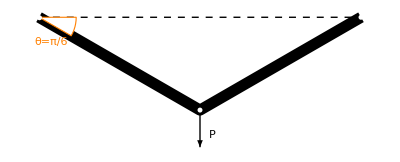

```mathematica
Unprotect[D,E];(*In Mathematica, D and E are reserved for derivative and exponential at default. "Unprotect" the letters first to assign our own values to them  *)
ClearAll[Tmag, Amag,P]; 

L=Quantity[15,"feet"]; (*Initial length of the bars*)
E=Quantity[30 10^6,("PoundsForce")/("Inches")^2]; (*Young's modulus of the bars*)
θ=π/6;
D=L Cos[θ]; 
H=L Sin[θ];

σw=Quantity[10000 ,("PoundsForce")/("Inches")^2];
P=Quantity[5000 ,"PoundsForce"];
T=Quantity[ Tmag,"PoundsForce"];
A= Quantity[Amag,("Inches")^2];

eq1=P==2T Sin[θ]; (*Force balance in the vertical direction*)
ineq1=T/A==σw ; (*Failure criterion*)

sol=Solve[eq1 && ineq1, {Tmag,Amag}]//N; (*Solve for the values of Tmag and Amag*)
{Tmag, Amag}={Tmag, Amag}/.sol[[1]]; (*If you aren't familiar with this step, try reading "https://reference.wolfram.com/language/howto/UseRuleSolutions.html"*)


δ= (T L)/(E A) (*change in length length*);
l=L+δ (*Final length*);
Δ=UnitConvert[(l^2-D^2)^(1/2)-H,"inches"](*displacement of the pin*)
```

0.11994 in